## <r^2(t)>, calcul numérique

### États propres dans la base atomique

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
ClearAll[t,v,r];
t[i_]:=Block[{k,tt},
k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]
```

```mathematica
(* hamiltonien avec conditions aux bords libres *)
Clear[h];
h[n_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
ar=SparseArray[tbl,{2^n,2^n}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* états propres et leurs énergies dans la base atomique *)
valvec[vv_,rr_,i_]:=Block[{v=vv,r=rr},
Eigensystem[h[i]]
]
```

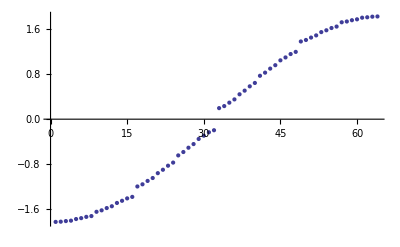

```mathematica
(* le spectre est bien comme on l'attend *)
ListPlot[Sort[valvec[.9,.9,6][[1]]]]
```

```mathematica
(* les vecteurs propres sont bien normalisés à 1 *)
Norm/@valvec[.1,.001,5][[2]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

### Propagateur retardé dans la base atomique

```mathematica
(* attention ! on fixe les couplages et la taille du système ! *)
K[t_,i_,j_]:=Block[{n=5,val,vec},
{val,vec}=valvec[0.9,0.9,n];
Sum[Exp[-I t val[[k]]]*vec[[k]][[i]]*Conjugate[vec[[k]][[j]]],{k,2^n}]
]
```

```mathematica
K[t,1,1]
```

0.0283643 ⅇ^((0.+0.221679 ⅈ) t)+0.0283643 ⅇ^((0.-0.221679 ⅈ) t)+0.0546403 ⅇ^((0.+0.326382 ⅈ) t)+0.0546403 ⅇ^((0.-0.326382 ⅈ) t)+0.0632905 ⅇ^((0.-0.476074 ⅈ) t)+0.0632905 ⅇ^((0.+0.476074 ⅈ) t)+0.0555473 ⅇ^((0.-0.608826 ⅈ) t)+0.0555473 ⅇ^((0.+0.608826 ⅈ) t)+0.052717 ⅇ^((0.-0.798553 ⅈ) t)+0.052717 ⅇ^((0.+0.798553 ⅈ) t)+0.0545766 ⅇ^((0.-0.922248 ⅈ) t)+0.0545766 ⅇ^((0.+0.922248 ⅈ) t)+0.0438649 ⅇ^((0.+1.06444 ⅈ) t)+0.0438649 ⅇ^((0.-1.06444 ⅈ) t)+0.0260023 ⅇ^((0.+1.16837 ⅈ) t)+0.0260023 ⅇ^((0.-1.16837 ⅈ) t)+0.0242751 ⅇ^((0.+1.39504 ⅈ) t)+0.0242751 ⅇ^((0.-1.39504 ⅈ) t)+0.0322041 ⅇ^((0.-1.46469 ⅈ) t)+0.0322041 ⅇ^((0.+1.46469 ⅈ) t)+0.0248127 ⅇ^((0.+1.55855 ⅈ) t)+0.0248127 ⅇ^((0.-1.55855 ⅈ) t)+0.0153141 ⅇ^((0.+1.62712 ⅈ) t)+0.0153141 ⅇ^((0.-1.62712 ⅈ) t)+0.0103816 ⅇ^((0.-1.72817 ⅈ) t)+0.0103816 ⅇ^((0.+1.72817 ⅈ) t)+0.0088314 ⅇ^((0.+1.76377 ⅈ) t)+0.0088314 ⅇ^((0.-1.76377 ⅈ) t)+0.00379727 ⅇ^((0.+1.80699 ⅈ) t)+0.00379727 ⅇ^((0.-1.80699 ⅈ) t)+0.00138049 ⅇ^((0.+1.8242 ⅈ) t)+0.00138049 ⅇ^((0.-1.8242 ⅈ) t)

### “Matrice T” dans la base atomique

```mathematica
(* on prend des distances entre sites ppv proportionnelles aux amplitudes de saut *)
Clear[d]
d=t;
```

```mathematica
(* attention ! on fixe les couplages et la taille du système ! *)
T[t_,i_,j_]:=Block[{n=5,v=0.9,r=0.9,val,vec},
{val,vec}=valvec[v,r,n];
Sum[d[k]*Exp[-I t val[[k]]]*vec[[k]][[i]]*Conjugate[vec[[k]][[j]]],{k,2^n}]
]
```

```mathematica
T[t,1,1]
```

0.0167488 ⅇ^((0.+0.221679 ⅈ) t)+0.0283643 ⅇ^((0.-0.221679 ⅈ) t)+0.0491762 ⅇ^((0.+0.326382 ⅈ) t)+0.0546403 ⅇ^((0.-0.326382 ⅈ) t)+0.0512653 ⅇ^((0.-0.476074 ⅈ) t)+0.0632905 ⅇ^((0.+0.476074 ⅈ) t)+0.0499926 ⅇ^((0.-0.608826 ⅈ) t)+0.0555473 ⅇ^((0.+0.608826 ⅈ) t)+0.0384307 ⅇ^((0.-0.798553 ⅈ) t)+0.052717 ⅇ^((0.+0.798553 ⅈ) t)+0.0491189 ⅇ^((0.-0.922248 ⅈ) t)+0.0545766 ⅇ^((0.+0.922248 ⅈ) t)+0.0355306 ⅇ^((0.+1.06444 ⅈ) t)+0.0438649 ⅇ^((0.-1.06444 ⅈ) t)+0.0234021 ⅇ^((0.+1.16837 ⅈ) t)+0.0260023 ⅇ^((0.-1.16837 ⅈ) t)+0.0159269 ⅇ^((0.+1.39504 ⅈ) t)+0.0242751 ⅇ^((0.-1.39504 ⅈ) t)+0.0289837 ⅇ^((0.-1.46469 ⅈ) t)+0.0322041 ⅇ^((0.+1.46469 ⅈ) t)+0.0200983 ⅇ^((0.+1.55855 ⅈ) t)+0.0248127 ⅇ^((0.-1.55855 ⅈ) t)+0.0137827 ⅇ^((0.+1.62712 ⅈ) t)+0.0153141 ⅇ^((0.-1.62712 ⅈ) t)+0.00756822 ⅇ^((0.-1.72817 ⅈ) t)+0.0103816 ⅇ^((0.+1.72817 ⅈ) t)+0.00794826 ⅇ^((0.+1.76377 ⅈ) t)+0.0088314 ⅇ^((0.-1.76377 ⅈ) t)+0.00307579 ⅇ^((0.+1.80699 ⅈ) t)+0.00379727 ⅇ^((0.-1.80699 ⅈ) t)+0.00124244 ⅇ^((0.+1.8242 ⅈ) t)+0.00138049 ⅇ^((0.-1.8242 ⅈ) t)

### <r^2(t)>_n

```mathematica
Clear[TT];
TT=ParallelTable[T[t,i,j],{i,2^5},{j,2^5}];
diff=ConjugateTranspose[TT].TT
```

{{(0.0167488 ⅇ^((0.+0.221679 ⅈ) t)+0.0283643 ⅇ^((0.-0.221679 ⅈ) t)+«28»+0.00124244 ⅇ^((0.+1.8242 ⅈ) t)+0.00138049 ⅇ^((0.-1.8242 ⅈ) t)) (0.0167488 ⅇ^((0.-«20» ⅈ) «9»[t])+«30»+0.00138049 ⅇ^(«1»))+«31»,«30»,«1»},«31»}

```mathematica
diff[[1,10]]/.t->2
```

0.0768519+1.06685×10^-16 ⅈ